Analisi della risposta libera per un sistema lineare tempo invariante tempo continuo

```mathematica
A=({{-5/2, 1/2, -1/2, 0}, {-1/2, -1/2, -7/2, -1/2}, {0, 1, -5, -1/2}, {1, -3, 11, 0}})
```

{{-5/2,1/2,-1/2,0},{-1/2,-1/2,-7/2,-1/2},{0,1,-5,-1/2},{1,-3,11,0}}

Calcolo gli autovalori

```mathematica
λ=Eigenvalues[A]
```

{-2,-2,-2,-2}

Calcolo la molteplicita’ geometrica di A,

```mathematica
NullSpace[A+2 IdentityMatrix[4]]
```

{{0,-1/4,-1/4,1}}

La matrice non e’ diagonalizzabile e, se la molteplicita’ geometrica e’ pari ad uno, avremo un unico blocco di Jordan di dimensione 4 x 4 che rappresenta la forma canonica di A

```mathematica
Factor[ResourceFunction["MatrixMinimalPolynomial"][A,x]]
```

(2+x)^4

Mi calcolo la matrice di cambiamento di base

```mathematica
Subscript[T, J]=JordanDecomposition[A][[1]]
```

{{0,0,1/4,-1/8},{-1/4,1/8,5/16,17/32},{-1/4,1/8,1/16,5/32},{1,0,0,0}}

```mathematica
Subscript[T, J]//MatrixForm
```

(0 | 0 | 1/4 | -1/8
-1/4 | 1/8 | 5/16 | 17/32
-1/4 | 1/8 | 1/16 | 5/32
1 | 0 | 0 | 0)

```mathematica
NullSpace[A+2 IdentityMatrix[4]]
```

{{0,-1/4,-1/4,1}}

Prendo la quarta colonna della matrice di cambiamento di base e la moltiplico (da sx) per A + 2 I

```mathematica
(A+2 IdentityMatrix[4]).Subscript[T, J][[All,4]]
```

{1/4,5/16,1/16,0}

Trovo questa strana proprieta’,  ed ora prendo la terza colonna della matrice e la moltiplico da sx per A + 2 I

```mathematica
(A+2 IdentityMatrix[4]).Subscript[T, J][[All,3]]
```

{0,1/8,1/8,0}

Trovo questa strana proprieta’,  ed ora prendo la seconda colonna della matrice e la moltiplico da sx per A + 2 I

```mathematica
(A+2 IdentityMatrix[4]).Subscript[T, J][[All,2]]
```

{0,-1/4,-1/4,1}

Considero lo stato iniziale

```mathematica
Subscript[x, 0]={{0},{1},{0},{0}}
```

{{0},{1},{0},{0}}

e lo proietto lungo le componenti della matrice di cambiamento di base

```mathematica
Subscript[z, 0]=Inverse[Subscript[T, J]].Subscript[x, 0]
```

{{0},{-3},{1},{2}}

```mathematica
Subscript[x, l][t_]:=Simplify[Subscript[T, J].({{ⅇ^(-2t), t ⅇ^(-2t), t^2/2 ⅇ^(-2t), t^3/6 ⅇ^(-2t)}, {0, ⅇ^(-2t), t ⅇ^(-2t), t^2/2 ⅇ^(-2t)}, {0, 0, ⅇ^(-2t), t ⅇ^(-2t)}, {0, 0, 0, ⅇ^(-2t)}}).Subscript[z, 0]]
```

```mathematica
Subscript[x, l][t]
```

{{1/2 ⅇ^(-2 t) t},{-1/12 ⅇ^(-2 t) (-12-18 t+t^3)},{-1/12 ⅇ^(-2 t) t (-12+t^2)},{1/6 ⅇ^(-2 t) t (-18+3 t+2 t^2)}}

```mathematica
Subscript[x, l][t]//MatrixForm
```

(1/2 ⅇ^(-2 t) t
-1/12 ⅇ^(-2 t) (-12-18 t+t^3)
-1/12 ⅇ^(-2 t) t (-12+t^2)
1/6 ⅇ^(-2 t) t (-18+3 t+2 t^2))

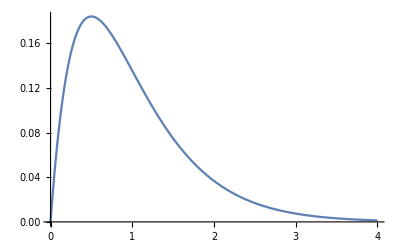

```mathematica
Plot[t ⅇ^(-2 t),{t,0,4},PlotRange->All]
```

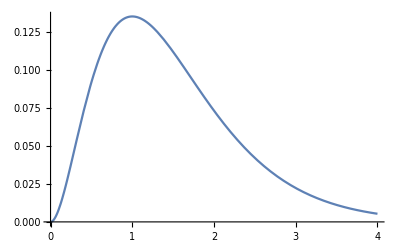

```mathematica
Plot[t^2 ⅇ^(-2 t),{t,0,4},PlotRange->All]
```

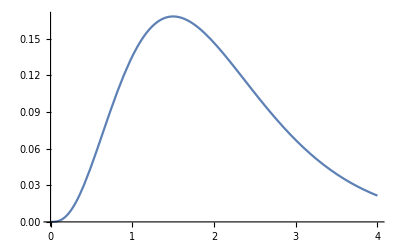

```mathematica
Plot[t^3 ⅇ^(-2 t),{t,0,4},PlotRange->All]
```

Mi calcolo l’uscita

```mathematica
Cc={1,-2,0,1}
```

{1,-2,0,1}

```mathematica
Cc.Subscript[T, J]
```

{3/2,-1/4,-3/8,-19/16}

```mathematica
Subscript[y, l][t_]:=Simplify[Cc.Subscript[x, l][t]]
```

```mathematica
Subscript[y, l][t]
```

{1/2 ⅇ^(-2 t) (-4-11 t+t^2+t^3)}

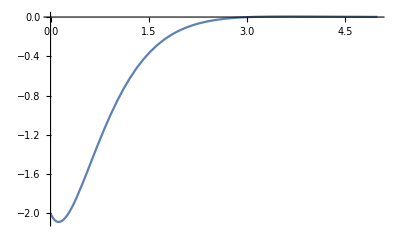

```mathematica
Plot[Subscript[y, l][t],{t,0,5},PlotRange->All]
```